```mathematica
(* Import or Create Raytracing Results *)
```

```mathematica
(* Set Up Computer Options *)
numkernel=4;
Unprotect[$ProcessorCount];
$ProcessorCount=numkernel;

(* ----- Command Line Running ----- *)
cmddata=$ScriptCommandLine;
dayinyear=ToExpression[cmddata[[2]]];
```

Part::partw: Part 2 of {} does not exist.

ToExpression::notstrbox: {}⟦2⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tomikbaikie/Dropbox (Cambridge University)/Physics/SimulationsLSC/Example_simulation/combined_LSC_directional

```mathematica
dayinyear = 200;
```

```mathematica
CreateDirectory["results_colorado"]
```

CreateDirectory::eexist: /Users/tomikbaikie/Dropbox (Cambridge University)/Physics/SimulationsLSC/Example_simulation/combined_LSC_directional/results_colorado already exists.

$Failed

```mathematica
month
```

6

```mathematica
(*Final day is 347*)
If[dayinyear < 24, {month = 1, dayinmonth = dayinyear},If[dayinyear < 47, {month = 2, dayinmonth = dayinyear - 23},If[dayinyear < 76, {month = 3, dayinmonth = dayinyear - 46},If[dayinyear < 107, {month = 4, dayinmonth = dayinyear - 75},If[dayinyear < 142, {month = 5, dayinmonth = dayinyear - 106},If[dayinyear < 177, {month = 6, dayinmonth = dayinyear - 141},If[dayinyear < 213, {month = 7, dayinmonth = dayinyear - 176},If[dayinyear < 246, {month = 8, dayinmonth = dayinyear - 212},If[dayinyear < 275, {month = 9, dayinmonth = dayinyear - 245},If[dayinyear < 302, {month = 10, dayinmonth = dayinyear - 274},If[dayinyear < 325, {month = 11, dayinmonth = dayinyear - 301}, {month = 12, dayinmonth = dayinyear - 324}]]]]]]]]]]];

spectralist=Import["./Denver/fullspectra2018"<>ToString[month]<>".mx"];

startpart = 1 + 150*(dayinmonth - 1);
endpart = If[startpart + 149 > Length[spectralist], Length[spectralist], startpart + 149];
```

```mathematica
Import["./raytracing.mx"];

(* needs to be edited for each simulation *) 
emissionmax=N[1200];
emissionmin=N[311];
wavelengthtable=Table[{N[x],0},{x,emissionmin,emissionmax,1}];
```

```mathematica
(* LSC Orientation  *)
```

```mathematica
(*LSC orientation; vector defining its surface normal in degrees*)
lscAltitude=90 ;(*0 is vertical, 90 is horizontal*)
lscAzimuth = 180;(*0 is facing North, 180 is facing South*)
```

```mathematica
sphericaltoCartesian[θ_,ϕ_]=FromSphericalCoordinates[{1,π/180.(90.-θ),-π+2π /360.ϕ}];(*shifted to our angle definition: normal definition is theta from 0 to pi, phi from -pi to pi*)
normDot[a_,b_]:=a.b/(Norm[a]Norm[b]);(*normed dotproduct to calculate the angle between sun angle and surface normal*)
realAngleAtLSC[ θ_, ϕ_] := (*effective angle between lsc and sun, we can do this since the lsc is symmetric in the plane*)
Module[{a, b},
a = sphericaltoCartesian[lscAltitude,lscAzimuth];
b =sphericaltoCartesian[θ,ϕ];(*this is the orientation of the surface normal of the LSC*)
90(*go from surface normal angle to surface angle*)- ArcCos[ normDot[a, b]]360./(2π)
  ];
```

```mathematica
(*Constants*)
```

```mathematica
c = 299792458.; (* units: m / s *)
h = 6.6260695729*10^-34//N; (* units: J s - Planck's Constant *)
h2 = 4.136 10^-15//N; (* units: eV s - Planck's Constant *)
q = 1.60217657*10^-19//N; (* units: Coulombs *)
k = 8.617 * 10^−5//N; (* units: eV / K *)
T = 298.15//N;(* units: K *)
fac = h c 10^9 /q//N (* convert nm to eV *);
k2= 1.3807 10^-23//N (*J/K*);
β=k T//N;
```

```mathematica
(*spectra conversion functions*)
```

```mathematica
(* Function to calculate the flux of a solar spectrum *)
(* units: A/(m^2 eV) *)
makeFlux[data_]:={ fac/#[[1]],(h c)/(fac/#[[1]])^2*#[[1]]/(h c) *#[[2]]}&/@data;
makeFluxnm[data_]:={#[[1]],q*#[[2]]*(#[[1]] 10^-9)/(h c)}&/@data;
unmakeFlux[data_]:={fac/#[[1]],#[[2]]*(h c)/(fac/#[[1]])*(fac/(fac/#[[1]]))^2/(h c)}&/@data;
unmakeFluxnm[data_]:={#[[1]],#[[2]]/q*(h c)/(#[[1]] 10^-9)}&/@data;


(*Temperature dependencies*)
```

```mathematica
(* Temperature dependent intrinsic charge carrier concentration from K. Misiakos, et al. Accurate Measurements of the Silicon Intrinsic Carrier Density from 78 to 340 K. J.Appl.Phys. 1993, 74, 3293–3297 DOI:10.1063/1.354551 *)
(* units: m^-3 *)
Sini[T_Real] := 5.29* 10^19 (T/300.)^2.54 Exp[-6726./T]*10^6;
```

```mathematica
(* Temperature dependent bandgap is calculated using Varshni’s empirical equation with values from the book Physics of Semiconductor Devices Physics of Semiconductor Devices, Wiley-Interscience, 1995 from Sze *)
(* units: eV *)
SiBandgap[T_Real] := 1.17 - 4.73*10^-4 T^2./(T+636.);
```

```mathematica
(* Temperature dependent Auger coefficient from J. Dziewior et al. Auger Coefficients for Highly Doped and Highly Excited Silicon. Appl.Phys.Lett. 1977, 346, 11–14 DOI:10.1063/1.89694 *)
(* Cn = 2.8 x 10^-31 cm^6/s Cp = 0.99 x 10^-31cm^6/s units: m^6/s *)
SiC[T_Real] := (2.8 + 0.99)*10^-43*(T/300.)^(1./2.);
```

```mathematica
(*Current densities*)
```

```mathematica
(* Generation current density *)
jgSi[EQE_] := Quiet[NIntegrate[ Interpolation[EQE,InterpolationOrder->0][En] Γ[En],{En,0.0,4.4}]];
```

```mathematica
(* Radiative recombination current density *)
JRad0Si = q 2 Pi/(c^2 h2^3)NIntegrate[  En^2/(Exp[En/( k T)]-1),{En,SiBandgap[T],4.4}];
JRSi[V_Real,Il_Real,Rs_Real]:=JRad0Si ( Exp[(V+Il*Rs*0.0001)/(k T)]-1);
```

```mathematica
(* Auger recombination current density *)
JRAuger[V_Real,Il_Real,Rs_Real,L_Real] :=  q L SiC[T] Sini[T]^3( Exp[(3 (V+Il*Rs*0.0001))/(2 k T)]-1);
```

```mathematica
(* Non-radiative recombination current density *)
JRnon[V_Real,Il_Real,Rs_Real,INR_Real] :=INR*10^-42 Sini[T]^2(Exp[(V+Il*Rs*0.0001)/( k T)]-1);
```

```mathematica
(* Resistance *)
Resistance[V_Real,Il_Real,Rs_Real,Rsh_Real] := (V+Il *Rs*0.0001)/(Rsh*0.0001);
```

```mathematica
(*Fitting values*)
```

```mathematica
(* Thickness of silicon for Auger recombination in m*)
thicknesses = {
(*1*) 1.7*10^-4,
(*2*) 1.8*10^-4, (* assumption *)
(*3*) 1.8*10^-4,
(*4*)  1.9*10^-4,
(*5*) 1.8*10^-4, (* assumption *)
(*6*)  1.8*10^-4, (* assumption *)
(*7*) 1.9*10^-4,
(*8*) 1.95*10^-4,
(*9*) 1.5*10^-4,
(*10*) 2*10^-4,
(*11*) 1.5*10^-4,
(*12*) 2*10^-4,
(*13*) 2*10^-4};
```

```mathematica
(* Parasitic resistances in ohm cm^2 *)
Rs={
(*1*) 1.48,
(*2*) 1.15,
(*3*) 1.35,
(*4*) 0.82,
(*5*)1.28,
(*6*) 0.73,
(*7*) 0.59,
(*8*) 0.6,
(*9*) 0.67,
(*10*) 0.75,
(*11*) 0.47,
(*12*)0.31,
(*13*)0.08};
Rsh={
(*1*) 1800,
(*2*) 1300,
(*3*) 1800,
(*4*) 1800,
(*5*) 1200,
(*6*) 2000,
(*7*) 2000,
(*8*) 3000,
(*9*) 2000,
(*10*) 800,
(*11*) 4000,
(*12*) 6000,
(*13*)10000};
```

```mathematica
(* Non-radiative recombination *)
INR={
(*1*) 58,
(*2*) 85.7,
(*3*) 56,
(*4*) 58,
(*5*) 10.5,
(*6*) 43,
(*7*) 35,
(*8*) 24.1,
(*9*) 1.5,
(*10*) 1.95,
(*11*) 1.7,
(*12*) 1.41,
(*13*) 1.88485};
```

```mathematica
(*Cell 13*)

(* Import JV characteristic*)
IV13 = Import["./Record_Si_cell/13_IV.csv"];
```

```mathematica
(* Import EQE *)
EQE13 = Import["./Record_Si_cell/13_EQE.csv"];
intEQE13=Interpolation[EQE13,InterpolationOrder->0];
```

```mathematica
(*Padding spectra with zeros*)
padZero[list_] := Union[Replace[Complement[Range[300, 1300, 1], list[[All, 1]]],x_ -> {x, 0}, {1}], list];
```

```mathematica
(* OG function *)
```

```mathematica
sicell[areasurface_,areaside_,side_Integer,pointinmonth_Integer]:= Module[{time,altitude,spectradirect,spectradiffuse,intspectradirect,intspectradiffuse,intfluxnmdirect,sidespectradirectint,intfluxnmdiffuse,concentration,totalincidentpowerdiffuse,totalconcentratedincidentpowerdiffuse,totalincidentpowerdirect,totalconcentratedincidentpowerdirect,totalfluxdiffuse,totalfluxdirect,LSCoutputlistdirect,sidespectrafluxdirect,LSCoutputlistdiffuse,sidespectrafluxdiffuse,sidespectradirect,sidespectradiffuse,outputpowerLSCdiffuse,outputpowerLSCdirect,JG,jg,dSi,totalefficiency,outputpowerLSC,LSCefficiency,efficiency,JGdirect},

numberofangles=89;
totalphotonsin=10000;
cell=13;


time=spectralist[[pointinmonth,1]];

incidentangle=Round[realAngleAtLSC[spectralist[[pointinmonth,2]],spectralist[[pointinmonth,-1]]],1];
(* altitude=Round[spectralist[[pointinmonth,2]],1]; *) 

spectradirect=spectralist[[pointinmonth,4]];
spectradiffuse=spectralist[[pointinmonth,5]];


intspectradirect=Interpolation[spectradirect,InterpolationOrder->0];
intspectradiffuse=Interpolation[spectradiffuse,InterpolationOrder->0];

(* this the the current FLUX per nm*) 
intfluxnmdirect=Interpolation[makeFluxnm[spectradirect],InterpolationOrder->0];
intfluxnmdiffuse=Interpolation[makeFluxnm[spectradiffuse],InterpolationOrder->0];

(* concentration factor of LSC *) 
concentration=N[areasurface/(4* areaside)];

(* Total Power DENSITY of the diffuse light *) 
totalincidentpowerdiffuse= Integrate[intspectradiffuse[wl],{wl,spectradiffuse[[1,1]],spectradiffuse[[-1,1]]}]; (*e.g. total AM1.5 power*) (*W/m^2*)
totalincidentpowerdirect = Integrate[intspectradirect[wl],{wl,spectradirect[[1,1]],spectradirect[[-1,1]]}]; (*e.g. total AM1.5 power*) (*W/m^2*)

(* Concentrated fluxes of light to compare vs a perfect LSC concentrator if required *) 
(* totalconcentratedincidentpowerdirect = concentration* totalincidentpowerdirect; (*e.g. Total AM1.5 power concentrated on the Si (7500W/m^2)*) *) 
(* totalconcentratedincidentpowerdiffuse =concentration* totalincidentpowerdiffuse; (*e.g. Total AM1.5 power concentrated on the Si (7500W/m^2)*) *) 

(* Charge FLUX  total *) 
totalfluxdiffuse=Integrate[intfluxnmdiffuse[j],{j,spectradiffuse[[1,1]],spectradiffuse[[-1,1]]}];(*total flux in spectrum (AM1.5G=689.833 A/m^2*)
totalfluxdirect=Integrate[intfluxnmdirect[j],{j,spectradirect[[1,1]],spectradirect[[-1,1]]}];(*total flux in spectrum (A/m^2*)


(* if the sun is above horizon *) 
If[incidentangle>=1,

(* this function related the ray tracing data to the output *) 
(* the output is determined by multiplying 
1. the input diffuse charge flux (intfluxnmdiffuse) in A/m^2 
2. time the concentration factor to account for the area of the LSC (dimensionless) 
2. the number of photons per wavelength per angle from packed the data (dimensionless) 
3. dividing that by the number of photons in the LSC simulation, giving an efficiency per angle 
4. we are interested in direct light at this specifc angle. 

resulting table is a table of wavelgnths vs  current flux density spectrum FROM the LSC for each input  *) 

(* resulting dimensions is wavelengths in and wavelengths out simulated, this relates the spectrum in to the spectrum out
it has dimensions of wavelength in at at each point a spectrum out 
 that is then scaled  *) 

WithCleanup[
SetSystemOptions["CompileOptions"->"TableCompileLength"->Infinity],
LSCoutputlistdirect=Table[{wlength,1/(totalphotonsin)*intfluxnmdirect[wlength]*Normal[raytracingdata[[side,incidentangle,wlength-emissionmin+1]]]} , {wlength, emissionmin, emissionmax,1}];,
SetSystemOptions["CompileOptions"->"TableCompileLength"->250]];


(* Now, LSCoutputlistdirect in terms in {input wavelenglth,{output spectra}}, what we need is the total output spectra {nm out, total}  *) 
outputmatrix =LSCoutputlistdirect[[;;,2]];
sidespectrafluxdirect=Table[{λ,Total[outputmatrix[[;;,λ-emissionmin+1]]]},{λ,wavelengthtable[[;;,1]]}];(*nm,A/(nm m^2)*)

(* this gives it instead of Current density flux, as power density flux per nm *) 
sidespectradirect=unmakeFluxnm[sidespectrafluxdirect]; (*nm,W/(nm m^2)*)

(* total power per unit area *) 
sidespectradirectint = Interpolation[sidespectradirect,InterpolationOrder->0];
outputpowerLSCdirect=Integrate[sidespectradirectint[x],{x,sidespectradirect[[1,1]],sidespectradirect[[-1,1]]}];

(* current density of the silicon solar cell is determined by multiplying EQE is in units of eV times this by the fluxs in A/(m^2 /eV) *) 
sidespectradirectinteV = Interpolation[makeFlux[sidespectradirect],InterpolationOrder->0];
JGdirect=NIntegrate[intEQE13[En]*sidespectradirectinteV[En],{En,fac/sidespectradirect[[-1,1]],fac/sidespectradirect[[1,1]]},MaxRecursion->10000,WorkingPrecision->4]; (*A/m^2*)
,
(*No direct when Sun is below the horizon*)
sidespectrafluxdirect= Table[{w, 0}, {w, 300, 1300}];
sidespectradirect= Table[{w, 0}, {w, 300, 1300}]; (*nm,W/(nm m^2)*)
outputpowerLSCdirect=0;
JGdirect=0;
incidentangle=0;
numberofangles=89;
];


(** Diffuse **)
(* similarly to direct output generation, but this time we look at the spectra from each angle, (because it is diffuse), so therefore we must also divide by number of angles *)
(*LSCoutputlistdiffuse = Table[padZero[{#[[1]],1/(numberofangles*totalphotonsin)*intfluxnmdiffuse[wlength]*#[[2]]} & /@ packedthedata[[side, angle, wlength - startwavelength + 1]]],{angle, Join[Range[1, altitude - 1, 1], Range[altitude + 1, 90,1]]}, {wlength, startwavelength, 1200, 1}];*)

anglerange = Join[Range[1,incidentangle-1,1],Range[incidentangle+1,90,1]];
WithCleanup[
SetSystemOptions["CompileOptions"->"TableCompileLength"->Infinity],
LSCoutputlistdiffuse=Table[{wlength,1/(totalphotonsin)*intfluxnmdiffuse[wlength]*Normal[raytracingdata[[side,angle,wlength-emissionmin+1]]]} , {wlength, wavelengthtable[[;;,1]]},{angle,anglerange}];,
SetSystemOptions["CompileOptions"->"TableCompileLength"->250]]; (*nm,A/(nm m^2)*)

optimizedoutputdiffuse=LSCoutputlistdiffuse;

(* this time total over both angles and wavelengths *) 
(* Now, LSCoutputlistdiffuse in terms in {input wavelenglth,angle,{output spectra}}, what we need is the total output spectra {nm out, total}  *) 
outputmatrix =LSCoutputlistdiffuse[[;;,;;,2]];
sidespectrafluxdiffuse=Table[{λ,Total[outputmatrix[[;;,;;,λ-emissionmin+1]],2]},{λ,wavelengthtable[[;;,1]]}]; (*nm,A/(nm m^2)*)

sidespectradiffuse=unmakeFluxnm[sidespectrafluxdiffuse];(*nm,W/(nm m^2)*)
sidespectradiffuseint = Interpolation[sidespectradiffuse,InterpolationOrder->0];

outputpowerLSCdiffuse=Integrate[sidespectradiffuseint[y],{y,sidespectradiffuse[[1,1]],sidespectradiffuse[[-1,1]]}];

outputpowerLSC= outputpowerLSCdiffuse + outputpowerLSCdirect; (*concentrated power (*W/(m^2)*)*)
sidespectradiffuseinteV = Interpolation[makeFlux[sidespectradiffuse],InterpolationOrder->0];

JGdiffuse = NIntegrate[intEQE13[En]*sidespectradiffuseinteV[En],{En,fac/sidespectradiffuse[[-1,1]],fac/sidespectradiffuse[[1,1]]},MaxRecursion->10000,WorkingPrecision->4];
(**** Silicon cell ****)
(* total current density impinging on the silicon is given by the sum of the diffuse and direct light *) 
jg=JGdiffuse+JGdirect;


(* Make JV characteristic *)
dSi=Table[{v1,FindRoot[Il==jg-JRSi[v1,Il,Rs[[cell]]]-JRAuger[v1,Il,Rs[[cell]],thicknesses[[cell]]]-JRnon[v1,Il,Rs[[cell]],INR[[cell]]]-Resistance[v1,Il,Rs[[cell]],Rsh[[cell]]],{Il,0},PrecisionGoal->5,MaxIterations->10000][[1,2]]},{v1,0,SiBandgap[T]-0.3,.005}];

ivSi=Interpolation[dSi,InterpolationOrder->0];
(* Calculate Voc *)
vocSi=FindRoot[ivSi[v],{v,SiBandgap[T]-0.4}][[1,2]];
(* Calculate Jsc *)
jscSi=ivSi[0]/10;(*mA/cm^2*)
(* Finding the maximum power conversion efficiency of the Si cell we add additional constraints that the voltage must be positive and to help NMaximize*)
eff=NMaximize[{100ivSi[V] V/outputpowerLSC,0<V<SiBandgap[T]-0.3},V];
efficiency=eff[[1]];(*efficiency of Si*)
maxvoltage=V/.eff[[2]];
maxcurrent=ivSi[maxvoltage];(*A/m^2*)

(*LSCefficiency=(outputpowerLSC/(totalconcentratedincidentpowerdiffuse+totalconcentratedincidentpowerdirect ))  100 (* efficiency of LSC, relative to surface area *);*)
(* power into the LSC vs power out of the side of LSC BEFORE impinging onto silicon cell 
outputpower LSC is in W/(m^2) as is totalincidentpowerdirect+totalincidentpowerdiffuse*) 
outputpowerlsc = areaside*outputpowerLSC;
inputpower = (areasurface*(totalincidentpowerdirect+totalincidentpowerdiffuse));
lscPCE = outputpowerlsc/inputpower;

(* si PCE is the PCE from the LSC output *) 
siPCE = (maxcurrent*maxvoltage)/outputpowerlsc;

(* efficiency of LSC & Si system, relative to surface area *)
totalefficiency=(maxcurrent*maxvoltage)/(areasurface*(totalincidentpowerdirect+totalincidentpowerdiffuse));

(* assume that the max current and the max voltage is consistent over the timestep size 
data is in 5 minute internvals, but we do 3 steps (set out in efficiency table which calls this function - this is therefore 15 minutes. 
  *) 
  (* maxcurrent*maxvoltage is the power, but we need to give this in hours.  
  times by a thousand to get kilowatt hours*) 
kwh=(maxcurrent*maxvoltage)*(15/60)/1000;

Print["return"];

Return[{month,pointinmonth,DateString[time],side,totalefficiency,lscPCE,siPCE,kwh,inputpower,outputpowerlsc,siPCE}]; 

];
```

```mathematica
pointinmonth=startpart;

numberofangles=89;
totalphotonsin=10000;
cell=13;

time=spectralist[[pointinmonth,1]];

incidentangle=Round[realAngleAtLSC[spectralist[[pointinmonth,2]],spectralist[[pointinmonth,-1]]],1];
incidentangle
```

55

```mathematica
(* altitude=Round[spectralist[[pointinmonth,2]],1]; *) 

spectradirect=spectralist[[pointinmonth,4]];
spectradiffuse=spectralist[[pointinmonth,5]];

intspectradirect=Interpolation[spectradirect,InterpolationOrder->0];
intspectradiffuse=Interpolation[spectradiffuse,InterpolationOrder->0];

(* this the the current FLUX per nm*) 
intfluxnmdirect=Interpolation[makeFluxnm[spectradirect],InterpolationOrder->0];
intfluxnmdiffuse=Interpolation[makeFluxnm[spectradiffuse],InterpolationOrder->0];


(* Total Power DENSITY of the diffuse light *) 
totalincidentpowerdiffuse= Integrate[intspectradiffuse[wl],{wl,spectradiffuse[[1,1]],spectradiffuse[[-1,1]]}]; (*e.g. total AM1.5 power*) (*W/m^2*)
totalincidentpowerdirect = Integrate[intspectradirect[wl],{wl,spectradirect[[1,1]],spectradirect[[-1,1]]}]; (*e.g. total AM1.5 power*) (*W/m^2*)
```

```mathematica
totalincidentpowerdiffuse+totalincidentpowerdirect
```

1019.95

```mathematica
DateString[time]
```

Fri 20 Jul 2018 14:25:00

```mathematica
Plot[{intspectradiffuse[wl],intspectradirect[wl]},{wl,290,1500}]
```

```mathematica
exporttablediffuse = Table[{wl,intspectradiffuse[wl]},{wl,290,1500,1}];
exporttabledirect = Table[{wl,intspectradirect[wl]},{wl,290,1500,1}];
Export["./plots_for_sanity_colorado/intspectradiffuse.csv",exporttablediffuse]
Export["./plots_for_sanity_colorado/intspectradirect.csv",exporttabledirect]
```

./plots_for_sanity_colorado/intspectradiffuse.csv

./plots_for_sanity_colorado/intspectradirect.csv

```mathematica
totalincidentpowerdiffuse
```

441.424

```mathematica
totalincidentpowerdirect
```

578.523

```mathematica
inputflux = totalincidentpowerdiffuse+totalincidentpowerdirect
```

```mathematica
totalincidentpowerdiffuse
```

441.424

```mathematica
totalincidentpowerdirect
```

578.523

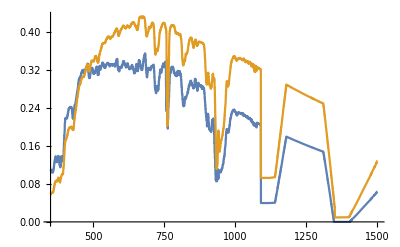

./plots_for_sanity_colorado/inputspectradiffuse.csv

./plots_for_sanity_colorado/inputspectradirect.csv

```mathematica
totalfluxdiffuse=Integrate[intfluxnmdiffuse[j],{j,spectradiffuse[[1,1]],spectradiffuse[[-1,1]]}];(*total flux in spectrum (AM1.5G=689.833 A/m^2*)
totalfluxdirect=Integrate[intfluxnmdirect[j],{j,spectradirect[[1,1]],spectradirect[[-1,1]]}];(*total flux in spectrum (A/m^2*)

Plot[{intfluxnmdiffuse[wl],intfluxnmdirect[wl]},{wl,350,1500}]

toexport=Table[{x,intfluxnmdiffuse[x]},{x,300,1200,1}];
Export["./plots_for_sanity_colorado/inputspectradiffuse.csv",toexport]
toexport=Table[{x,intfluxnmdirect[x]},{x,300,1200,1}];
Export["./plots_for_sanity_colorado/inputspectradirect.csv",toexport]
```

```mathematica
WithCleanup[
SetSystemOptions["CompileOptions"->"TableCompileLength"->Infinity],
LSCoutputlistdirect=Table[{wlength,1/(totalphotonsin)*intfluxnmdirect[wlength]*Normal[raytracingdata[[side,incidentangle,wlength-emissionmin+1]]]} , {wlength, emissionmin, emissionmax,1}];,
SetSystemOptions["CompileOptions"->"TableCompileLength"->250]];
```

```mathematica
WithCleanup[
SetSystemOptions["CompileOptions"->"TableCompileLength"->Infinity],
LSCoutputlistdirectside1=Table[{wlength,1/(totalphotonsin)*intfluxnmdirect[wlength]*Normal[raytracingdata[[1,incidentangle,wlength-emissionmin+1]]]} , {wlength, emissionmin, emissionmax,1}];
LSCoutputlistdirectside2=Table[{wlength,1/(totalphotonsin)*intfluxnmdirect[wlength]*Normal[raytracingdata[[2,incidentangle,wlength-emissionmin+1]]]} , {wlength, emissionmin, emissionmax,1}];
LSCoutputlistdirectside3=Table[{wlength,1/(totalphotonsin)*intfluxnmdirect[wlength]*Normal[raytracingdata[[3,incidentangle,wlength-emissionmin+1]]]} , {wlength, emissionmin, emissionmax,1}];
LSCoutputlistdirectside4=Table[{wlength,1/(totalphotonsin)*intfluxnmdirect[wlength]*Normal[raytracingdata[[4,incidentangle,wlength-emissionmin+1]]]} , {wlength, emissionmin, emissionmax,1}];,
SetSystemOptions["CompileOptions"->"TableCompileLength"->250]];
```

```mathematica
(* Now, LSCoutputlistdirect in terms in {input wavelenglth,{output spectra}}, what we need is the total output spectra {nm out, total}  *) 
outputmatrix =LSCoutputlistdirectside1[[;;,2]];
sidespectrafluxdirect1=Table[{λ,Total[outputmatrix[[;;,λ-emissionmin+1]]]},{λ,wavelengthtable[[;;,1]]}];(*nm , A/(nm m^2)*)
outputmatrix =LSCoutputlistdirectside2[[;;,2]];
sidespectrafluxdirect2=Table[{λ,Total[outputmatrix[[;;,λ-emissionmin+1]]]},{λ,wavelengthtable[[;;,1]]}];
outputmatrix =LSCoutputlistdirectside3[[;;,2]];
sidespectrafluxdirect3=Table[{λ,Total[outputmatrix[[;;,λ-emissionmin+1]]]},{λ,wavelengthtable[[;;,1]]}];
outputmatrix =LSCoutputlistdirectside4[[;;,2]];
sidespectrafluxdirect4=Table[{λ,Total[outputmatrix[[;;,λ-emissionmin+1]]]},{λ,wavelengthtable[[;;,1]]}];
```

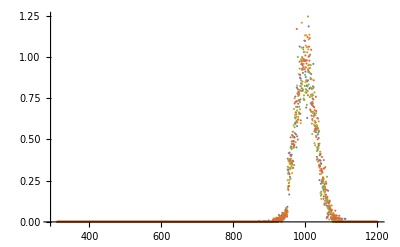

```mathematica
ListPlot[{unmakeFluxnm[sidespectrafluxdirect1],unmakeFluxnm[sidespectrafluxdirect2],unmakeFluxnm[sidespectrafluxdirect3],unmakeFluxnm[sidespectrafluxdirect4]},PlotRange->All] (* in W/m^2*)
```

```mathematica
outputdirectflux = unmakeFluxnm[sidespectrafluxdirect1];
outputdirectflux[[;;,2]]=outputdirectflux[[;;,2]]+unmakeFluxnm[sidespectrafluxdirect2][[;;,2]]+unmakeFluxnm[sidespectrafluxdirect3][[;;,2]]+unmakeFluxnm[sidespectrafluxdirect4][[;;,2]];
```

```mathematica
poweroutputdirect
```

InterpolatingFunction[…]

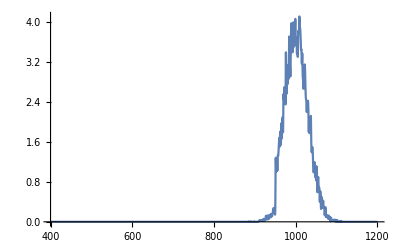

271.053

./plots_for_sanity_colorado/intspectradirect.csv

```mathematica
poweroutputdirect = Interpolation[outputdirectflux];
Plot[poweroutputdirect[x],{x,400,1200},PlotRange->All]
(* efficiency *)

toexport=Table[{x,poweroutputdirect[x]},{x,400,1200,1}];
NIntegrate[poweroutputdirect[x],{x,400,1200}]
Export["./plots_for_sanity_colorado/intspectradirect.csv",toexport]
```

```mathematica
(* total power per unit area *) 
sidespectradirectint = Interpolation[outputdirectflux,InterpolationOrder->0];
outputpowerLSCdirect=Integrate[sidespectradirectint[x],{x,sidespectradirect[[1,1]],sidespectradirect[[-1,1]]}]

(* current density of the silicon solar cell is determined by multiplying EQE is in units of eV times this by the fluxs in A/(m^2 /eV) *) 
sidespectradirectinteV = Interpolation[makeFlux[outputdirectflux],InterpolationOrder->0];
JGdirect=NIntegrate[intEQE13[En]*sidespectradirectinteV[En],{En,fac/sidespectradirect[[-1,1]],fac/sidespectradirect[[1,1]]},MaxRecursion->10000,WorkingPrecision->4](*A/m^2*)
```

271.053

206.7

```mathematica
(** Diffuse **)
(* similarly to direct output generation, but this time we look at the spectra from each angle, (because it is diffuse), so therefore we must also divide by number of angles *)
(*LSCoutputlistdiffuse = Table[padZero[{#[[1]],1/(numberofangles*totalphotonsin)*intfluxnmdiffuse[wlength]*#[[2]]} & /@ packedthedata[[side, angle, wlength - startwavelength + 1]]],{angle, Join[Range[1, altitude - 1, 1], Range[altitude + 1, 90,1]]}, {wlength, startwavelength, 1200, 1}];*)

anglerange = Join[Range[1,incidentangle-1,1],Range[incidentangle+1,90,1]];
WithCleanup[
SetSystemOptions["CompileOptions"->"TableCompileLength"->Infinity],
LSCoutputlistdiffuse1=Table[{wlength,1/(90*totalphotonsin)*intfluxnmdiffuse[wlength]*Normal[raytracingdata[[1,angle,wlength-emissionmin+1]]]} , {wlength, wavelengthtable[[;;,1]]},{angle,anglerange}];
LSCoutputlistdiffuse2=Table[{wlength,1/(90*totalphotonsin)*intfluxnmdiffuse[wlength]*Normal[raytracingdata[[2,angle,wlength-emissionmin+1]]]} , {wlength, wavelengthtable[[;;,1]]},{angle,anglerange}];
LSCoutputlistdiffuse3=Table[{wlength,1/(90*totalphotonsin)*intfluxnmdiffuse[wlength]*Normal[raytracingdata[[3,angle,wlength-emissionmin+1]]]} , {wlength, wavelengthtable[[;;,1]]},{angle,anglerange}];
LSCoutputlistdiffuse4=Table[{wlength,1/(90*totalphotonsin)*intfluxnmdiffuse[wlength]*Normal[raytracingdata[[4,angle,wlength-emissionmin+1]]]} , {wlength, wavelengthtable[[;;,1]]},{angle,anglerange}];,
SetSystemOptions["CompileOptions"->"TableCompileLength"->250]]; (*nm,A/(nm m^2)*)

(* this time total over both angles and wavelengths *) 
(* Now, LSCoutputlistdiffuse in terms in {input wavelenglth,angle,{output spectra}}, what we need is the total output spectra {nm out, total}  *) 
outputmatrix =LSCoutputlistdiffuse1[[;;,;;,2]];
sidespectrafluxdiffuse1=Table[{λ,Total[outputmatrix[[;;,;;,λ-emissionmin+1]],2]},{λ,wavelengthtable[[;;,1]]}]; (*nm,A/(nm m^2)*)
outputmatrix =LSCoutputlistdiffuse2[[;;,;;,2]];
sidespectrafluxdiffuse2=Table[{λ,Total[outputmatrix[[;;,;;,λ-emissionmin+1]],2]},{λ,wavelengthtable[[;;,1]]}]; (*nm,A/(nm m^2)*)
outputmatrix =LSCoutputlistdiffuse3[[;;,;;,2]];
sidespectrafluxdiffuse3=Table[{λ,Total[outputmatrix[[;;,;;,λ-emissionmin+1]],2]},{λ,wavelengthtable[[;;,1]]}]; (*nm,A/(nm m^2)*)
outputmatrix =LSCoutputlistdiffuse4[[;;,;;,2]];
sidespectrafluxdiffuse4=Table[{λ,Total[outputmatrix[[;;,;;,λ-emissionmin+1]],2]},{λ,wavelengthtable[[;;,1]]}]; (*nm,A/(nm m^2)*)
```

```mathematica
sidespectradiffuse1=unmakeFluxnm[sidespectrafluxdiffuse1];(*nm,W/(nm m^2)*)
sidespectradiffuse2=unmakeFluxnm[sidespectrafluxdiffuse2];
sidespectradiffuse3=unmakeFluxnm[sidespectrafluxdiffuse3];
sidespectradiffuse4=unmakeFluxnm[sidespectrafluxdiffuse4];

sidespectradiffuse=sidespectradiffuse1;
sidespectradiffuse[[;;,2]]=sidespectradiffuse1[[;;,2]]+sidespectradiffuse3[[;;,2]]+sidespectradiffuse2[[;;,2]]+sidespectradiffuse4[[;;,2]];

sidespectradiffuseint = Interpolation[sidespectradiffuse,InterpolationOrder->0];
```

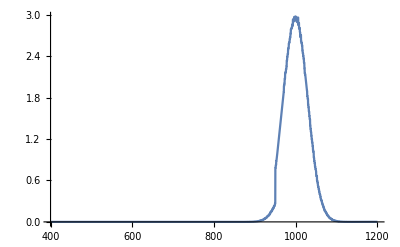

214.701

./plots_for_sanity_colorado/intspectradiffuse.csv

```mathematica
Plot[sidespectradiffuseint[x],{x,400,1200},PlotRange->All]
toexport=Table[{x,sidespectradiffuseint[x]},{x,400,1200,1}];
NIntegrate[sidespectradiffuseint[x],{x,400,1200}]
Export["./plots_for_sanity_colorado/intspectradiffuse.csv",toexport]
```

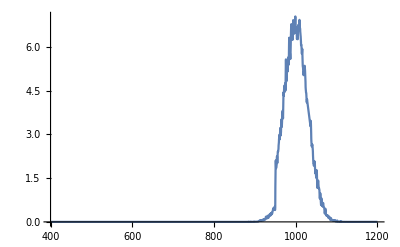

```mathematica
Plot[sidespectradiffuseint[x]+poweroutputdirect[x],{x,400,1200},PlotRange->All]
toexport=Table[{x,sidespectradiffuseint[x]+poweroutputdirect[x]},{x,400,1200,1}];
NIntegrate[sidespectradiffuseint[x]+poweroutputdirect[x],{x,400,1200}]
Export["./plots_for_sanity_colorado/totaloutput.csv",toexport]
```

```mathematica
485.7543122869873/1020
```

```mathematica
NIntegrate[sidespectradiffuseint[x],{x,400,1200}]/totalfluxdiffuse
```

0.793477

```mathematica
NIntegrate[poweroutputdirect[x],{x,400,1200}]/totalfluxdirect
```

0.625224

```mathematica
Plot[sidespectradiffuseint[x]+poweroutputdirect[x],{x,400,1200},PlotRange->All]
```

-Graphics-

```mathematica
outputpowerLSCdiffuse=Integrate[sidespectradiffuseint[y],{y,sidespectradiffuse[[1,1]],sidespectradiffuse[[-1,1]]}]

outputpowerLSC= outputpowerLSCdiffuse + outputpowerLSCdirect; (*concentrated power (*W/(m^2)*)*)
sidespectradiffuseinteV = Interpolation[makeFlux[sidespectradiffuse],InterpolationOrder->0];

JGdiffuse = NIntegrate[intEQE13[En]*sidespectradiffuseinteV[En],{En,fac/sidespectradiffuse[[-1,1]],fac/sidespectradiffuse[[1,1]]},MaxRecursion->10000,WorkingPrecision->4];
```

214.701

```mathematica
(**** Silicon cell ****)
(* total current density impinging on the silicon is given by the sum of the diffuse and direct light *) 
jg=JGdiffuse+JGdirect
```

370.3

```mathematica
(* Make JV characteristic *)
dSi=Table[{v1,FindRoot[Il==jg-JRSi[v1,Il,Rs[[cell]]]-JRAuger[v1,Il,Rs[[cell]],thicknesses[[cell]]]-JRnon[v1,Il,Rs[[cell]],INR[[cell]]]-Resistance[v1,Il,Rs[[cell]],Rsh[[cell]]],{Il,0},PrecisionGoal->5,MaxIterations->10000][[1,2]]},{v1,0,SiBandgap[T]-0.3,.005}];

ivSi=Interpolation[dSi,InterpolationOrder->1];
(* Calculate Voc *)
vocSi=FindRoot[ivSi[v],{v,SiBandgap[T]-0.4}][[1,2]];
(* Calculate Jsc *)
jscSi=ivSi[0]/10;(*mA/cm^2*)
(* Finding the maximum power conversion efficiency of the Si cell we add additional constraints that the voltage must be positive and to help NMaximize*)
eff=NMaximize[{100ivSi[V] V/outputpowerLSC,0<V<SiBandgap[T]-0.3},V];
```

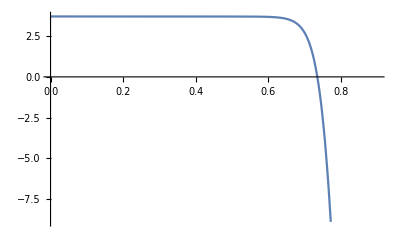

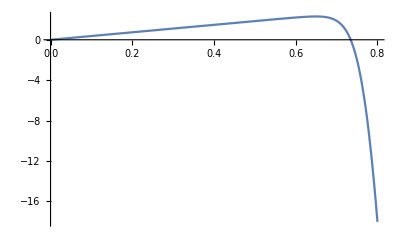

InterpolatingFunction::dmval: Input value {0.83} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.84} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.85} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.83} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.84} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.85} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
areasurface=0.1*0.1;

Plot[ivSi[x]*areasurface,{x,0,0.9}]
Plot[areasurface*ivSi[x] *x,{x,0,0.8},PlotRange->All]

ivcurve=Table[{x,ivSi[x]*areasurface},{x,0,0.9,0.01}];
powercurve =Table[{x,areasurface*ivSi[x] *x},{x,0,0.9,0.01}];

Export["./plots_for_sanity_colorado/powercurve.csv",powercurve];
Export["./plots_for_sanity_colorado/ivcurve.csv",ivcurve];
```

```mathematica
inputpower = (totalincidentpowerdirect+totalincidentpowerdiffuse)
```

1019.95

```mathematica
outputpowerlsc = outputpowerLSC
```

485.754

```mathematica
maxcurrent*maxvoltage/
```

2.3089

```mathematica
siPCE
```

0.475323

```mathematica
efficiency=eff[[1]];(*efficiency of Si*)
maxvoltage=V/.eff[[2]];
maxcurrent=ivSi[maxvoltage];(*A/m^2*)

(*LSCefficiency=(outputpowerLSC/(totalconcentratedincidentpowerdiffuse+totalconcentratedincidentpowerdirect ))  100 (* efficiency of LSC, relative to surface area *);*)
(* power into the LSC vs power out of the side of LSC BEFORE impinging onto silicon cell 
outputpower LSC is in W/(m^2) as is totalincidentpowerdirect+totalincidentpowerdiffuse*) 
outputpowerlsc = outputpowerLSC;
inputpower = (totalincidentpowerdirect+totalincidentpowerdiffuse);
lscPCE = outputpowerlsc/inputpower

(* si PCE is the PCE from the LSC output *) 
siPCE = (maxcurrent*maxvoltage)/outputpowerlsc

(* efficiency of LSC & Si system, relative to surface area *)
totalefficiency=(maxcurrent*maxvoltage)/((totalincidentpowerdirect+totalincidentpowerdiffuse))

(* assume that the max current and the max voltage is consistent over the timestep size 
data is in 5 minute internvals, but we do 3 steps (set out in efficiency table which calls this function - this is therefore 15 minutes. 
  *) 
  (* maxcurrent*maxvoltage is the power, but we need to give this in hours.  
  times by a thousand to get kilowatt hours*) 
kwh=(maxcurrent*maxvoltage)*(15/60)/1000;
```

0.476254

0.475323

0.226375

```mathematica
totalefficiency
```

0.226375

```mathematica
efficiencies=Table[sicell[(10* 10^-2)^2,10*1/3*(10^-2)^2,side,part],{part,startpart,endpart,3},{side,1,4}];
Export["./results_colorado/results_"<>ToString[month]<>"_"<>ToString[startpart]<>"_"<>ToString[endpart]<>".csv",efficiencies,"CSV"];
```

```mathematica
nb=InputNotebook[];
fn=FileNameJoin[{"analysis_denver_dot_LSC.wls"}];
FrontEndExecute[FrontEndToken[nb,"Save",{fn,"Text"}]]
```